```mathematica
Table[allGraphs[k,"dist"]=0,{k,atomKeys}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
SetDistance[]:=Block[{},
Table[
If[!KeyExistsQ[allGraphs[k],"dist"],
Table[
If[KeyExistsQ[allGraphs[child],"dist"],
If[!KeyExistsQ[allGraphs[k],"dist"],
allGraphs[k,"dist"]=allGraphs[child,"dist"]+1,
allGraphs[k,"dist"]=Max[allGraphs[k,"dist"],allGraphs[child,"dist"]+1]
]
];
,{child,Flatten[allGraphs[k,"children"]]}
]
],
{k,Keys[allGraphs]}
]
]
```

```mathematica
Select[Keys[allGraphs],!KeyExistsQ[allGraphs[#],"dist"]&]//Length
```

0

```mathematica
SetDistance[];
```

```mathematica
Tally[Table[allGraphs[k,"dist"],{k,Keys[allGraphs]}]]//Sort
```

{{0,52},{1,170},{2,307},{3,395},{4,388},{5,304},{6,182},{7,74},{8,19},{9,3},{10,1}}

```mathematica
Table[allGraphs[k,"distnull"]=0,{k,nullAtomKeys}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
SetDistanceNull[]:=Block[{},
Table[
If[!KeyExistsQ[allGraphs[k],"distnull"],
Table[
If[KeyExistsQ[allGraphs[child],"distnull"],
If[!KeyExistsQ[allGraphs[k],"distnull"],
allGraphs[k,"distnull"]=allGraphs[child,"distnull"]+1,
allGraphs[k,"distnull"]=Max[allGraphs[k,"distnull"],allGraphs[child,"distnull"]+1]
]
];
,{child,Flatten[allGraphs[k,"children"]]}
]
],
{k,Keys[allGraphs]}
]
]
```

```mathematica
SetDistanceNull[];
```

```mathematica
Tally[Table[allGraphs[k,"distnull"],{k,Keys[allGraphs]}]]//Sort
```

{{0,52},{1,39},{2,67},{3,143},{4,216},{5,244},{6,178},{7,74},{8,11},{Missing[KeyAbsent,distnull],871}}

```mathematica
Table[Flatten[allGraphs[k,"children"]]//Length,{k,Select[Keys[allGraphs],!KeyExistsQ[allGraphs[#],"distnull"]&]}]//Flatten
```

{0,0,4,0,0,4,4,2,0,0,6,2,6,2,0,0,0,4,2,6,6,4,4,8,10,6,2,0,0,0,4,6,0,0,6,4,6,8,8,2,6,6,4,4,8,10,6,4,6,8,8,8,4,10,8,8,6,6,10,6,6,10,10,6,4,2,0,0,0,2,4,0,0,4,2,4,4,4,6,2,8,4,8,4,2,6,12,8,4,2,6,8,2,8,6,10,12,8,6,10,10,6,12,8,10,6,4,2,0,0,0,2,4,0,0,4,2,4,4,4,2,0,0,8,6,4,6,8,4,8,6,8,2,6,4,2,4,8,8,6,12,8,4,2,2,6,8,6,8,10,8,6,6,10,12,10,8,12,10,8,6,4,6,8,4,8,6,8,4,8,8,12,14,10,6,4,4,8,10,8,12,12,6,10,10,14,14,10,6,4,2,0,0,0,2,4,0,0,4,2,4,4,4,2,0,0,8,6,4,6,8,4,8,6,8,8,2,0,0,0,6,10,8,6,4,4,6,8,6,8,8,8,6,12,10,8,8,10,12,10,12,12,2,6,4,2,8,4,2,2,6,8,6,6,10,4,8,8,6,12,8,6,8,10,12,10,8,12,10,8,6,4,4,6,8,6,8,8,4,8,10,6,4,4,8,6,10,8,12,14,10,8,12,12,10,14,14,10,8,6,4,4,6,8,6,8,8,8,6,12,10,8,8,10,12,10,12,12,8,4,6,4,4,10,6,10,8,10,8,12,8,14,12,12,14,10,14,12,10,8,8,10,12,10,12,12,6,6,10,6,6,10,10,12,8,8,12,10,14,8,12,10,14,14,10,12,12,16,12,12,16,16,18,14,10,6,4,2,0,0,0,2,4,0,0,4,2,4,4,4,2,0,0,8,6,4,6,8,4,8,6,8,8,2,0,0,0,6,10,8,6,4,4,6,8,6,8,8,8,6,12,10,8,8,10,12,10,12,12,14,8,2,0,0,0,6,8,0,0,8,6,8,12,12,14,10,8,6,4,4,6,8,6,8,8,8,6,12,10,8,8,10,12,10,12,12,14,8,6,8,12,12,14,12,10,8,10,12,8,12,10,12,14,12,12,16,14,12,12,12,14,16,12,12,16,14,16,16,16,2,2,6,2,2,6,6,8,4,4,8,6,10,4,8,6,10,10,6,8,8,12,8,8,12,12,10,8,6,4,4,6,8,6,8,8,8,4,6,4,4,10,6,10,8,10,8,12,8,14,12,12,14,10,14,10,8,6,4,4,6,8,6,8,8,8,6,12,10,8,8,10,12,10,12,12,4,8,10,6,4,4,8,6,10,8,12,14,10,8,12,12,10,14,14,12,10,8,8,10,12,10,12,12,6,10,8,6,12,8,6,6,10,12,10,10,14,8,12,12,10,16,12,10,12,14,16,14,12,16,18,14,10,8,6,4,4,6,8,6,8,8,8,6,12,10,8,8,10,12,10,12,12,14,8,6,8,12,12,14,12,10,8,10,12,8,12,10,12,14,12,12,16,14,12,12,12,14,16,12,12,16,14,16,16,16,4,8,8,12,14,10,6,4,4,8,10,8,12,12,6,10,10,14,14,12,10,8,10,12,8,12,10,12,6,10,8,6,8,12,12,10,16,12,8,6,6,10,12,10,12,14,12,10,10,14,16,14,12,16,18,14,12,10,8,10,12,8,12,10,12,14,12,12,16,14,12,12,12,14,16,12,12,16,14,16,16,16,10,6,12,8,12,8,6,10,16,12,8,6,10,12,6,12,10,14,16,12,10,14,14,10,16,12,18,16,14,12,12,12,14,16,12,12,16,14,16,16,16,8,8,12,8,8,12,12,10,8,8,14,10,14,10,8,8,8,12,10,14,14,12,12,16,18,14,10,8,8,8,12,14,8,8,14,12,14,16,16,10,14,14,12,12,16,18,14,12,14,16,16,16,12,18,16,16,14,14,18,14,14,18,18}

```mathematica
demoValues ={v1x2x3x4x5->0,v1x2x3x45->10,v1x2x35x4->4,v1x2x34x5->12,v1x2x345->18,v1x25x3x4->10,v1x25x34->16,v1x24x3x5->12,v1x24x35->8,v1x245x3->14,v1x23x4x5->12,v1x23x45->16,v1x235x4->12,v1x234x5->28,v1x2345->20,v15x2x3x4->6,v15x2x34->14,v15x24x3->12,v15x23x4->14,v15x234->20,v14x2x3x5->10,v14x2x35->6,v14x25x3->12,v14x23x5->16,v14x235->8,v145x2x3->20,v145x23->22,v13x2x4x5->4,v13x2x45->8,v13x25x4->6,v13x24x5->8,v13x245->6,v135x2x4->10,v135x24->8,v134x2x5->12,v134x25->8,v1345x2->18,v12x3x4x5->10,v12x3x45->16,v12x35x4->8,v12x34x5->16,v12x345->14,v125x3x4->20,v125x34->22,v124x3x5->14,v124x35->6,v1245x3->18,v123x4x5->18,v123x45->14,v1235x4->18,v1234x5->20,v12345->18}
```

{v1x2x3x4x5→0,v1x2x3x45→10,v1x2x35x4→4,v1x2x34x5→12,v1x2x345→18,v1x25x3x4→10,v1x25x34→16,v1x24x3x5→12,v1x24x35→8,v1x245x3→14,v1x23x4x5→12,v1x23x45→16,v1x235x4→12,v1x234x5→28,v1x2345→20,v15x2x3x4→6,v15x2x34→14,v15x24x3→12,v15x23x4→14,v15x234→20,v14x2x3x5→10,v14x2x35→6,v14x25x3→12,v14x23x5→16,v14x235→8,v145x2x3→20,v145x23→22,v13x2x4x5→4,v13x2x45→8,v13x25x4→6,v13x24x5→8,v13x245→6,v135x2x4→10,v135x24→8,v134x2x5→12,v134x25→8,v1345x2→18,v12x3x4x5→10,v12x3x45→16,v12x35x4→8,v12x34x5→16,v12x345→14,v125x3x4→20,v125x34→22,v124x3x5→14,v124x35→6,v1245x3→18,v123x4x5→18,v123x45→14,v1235x4→18,v1234x5→20,v12345→18}

```mathematica
nullDemoValues=Table[allGraphs[k,"colofournull"]->(allGraphs[k,"colofour"]/.demoValues),{k,nullAtomKeys}]
```

{p1x2x3x4x5→672,p1x2x3x45→440,p1x2x35x4→496,p1x2x34x5→416,p1x2x345→184,p1x25x3x4→464,p1x25x34→292,p1x24x3x5→460,p1x24x35→344,p1x245x3→172,p1x23x4x5→416,p1x23x45→274,p1x235x4→184,p1x234x5→160,p1x2345→30,p15x2x3x4→432,p15x2x34→268,p15x24x3→296,p15x23x4→268,p15x234→104,p14x2x3x5→464,p14x2x35→344,p14x25x3→320,p14x23x5→292,p14x235→128,p145x2x3→184,p145x23→114,p13x2x4x5→496,p13x2x45→328,p13x25x4→344,p13x24x5→344,p13x245→128,p135x2x4→224,p135x24→156,p134x2x5→184,p134x25→128,p1345x2→44,p12x3x4x5→440,p12x3x45→288,p12x35x4→328,p12x34x5→274,p12x345→122,p125x3x4→184,p125x34→114,p124x3x5→172,p124x35→128,p1245x3→32,p123x4x5→184,p123x45→122,p1235x4→44,p1234x5→30,p12345→0}

```mathematica
nullDemoValues=Table[allGraphs[k,"colofournull"]->(allGraphs[k,"colofour"]/.demoValues),{k,nullAtomKeys}]
```

{p1x2x3x4x5→3728,p1x2x3x45→2520,p1x2x35x4→3000,p1x2x34x5→2488,p1x2x345→1280,p1x25x3x4→2852,p1x25x34→1940,p1x24x3x5→2852,p1x24x35→2324,p1x245x3→1292,p1x23x4x5→2348,p1x23x45→1590,p1x235x4→1268,p1x234x5→1108,p1x2345→264,p15x2x3x4→2384,p15x2x34→1596,p15x24x3→1848,p15x23x4→1500,p15x234→712,p14x2x3x5→2616,p14x2x35→2120,p14x25x3→1996,p14x23x5→1682,p14x235→894,p145x2x3→1112,p145x23→702,p13x2x4x5→2640,p13x2x45→1772,p13x25x4→2038,p13x24x5→2050,p13x245→912,p135x2x4→1112,p135x24→870,p134x2x5→976,p134x25→746,p1345x2→224,p12x3x4x5→2360,p12x3x45→1558,p12x35x4→1924,p12x34x5→1598,p12x345→796,p125x3x4→980,p125x34→672,p124x3x5→1060,p124x35→870,p1245x3→230,p123x4x5→980,p123x45→628,p1235x4→186,p1234x5→182,p12345→0}

```mathematica
Select[Keys[allGraphs],allGraphs[#]["children"]=={}&]
```

{29524,29525,29527,29533,29537,29551,29560,29605,29608,29633,29767,29768,29797,29857,29888,30253,30262,30334,30496,30586,31711,31714,31738,31954,31984,32441,32684,36085,36086,36112,36166,36194,36817,36898,38281,38308,39014,49207,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],allGraphs[#]["children"]=={}&]}]
```

{-Graphics-29524,-Graphics-29525,-Graphics-29527,-Graphics-29533,-Graphics-29537,-Graphics-29551,-Graphics-29560,-Graphics-29605,-Graphics-29608,-Graphics-29633,-Graphics-29767,-Graphics-29768,-Graphics-29797,-Graphics-29857,-Graphics-29888,-Graphics-30253,-Graphics-30262,-Graphics-30334,-Graphics-30496,-Graphics-30586,-Graphics-31711,-Graphics-31714,-Graphics-31738,-Graphics-31954,-Graphics-31984,-Graphics-32441,-Graphics-32684,-Graphics-36085,-Graphics-36086,-Graphics-36112,-Graphics-36166,-Graphics-36194,-Graphics-36817,-Graphics-36898,-Graphics-38281,-Graphics-38308,-Graphics-39014,-Graphics-49207,-Graphics-49208,-Graphics-49210,-Graphics-49216,-Graphics-49220,-Graphics-49963,-Graphics-49972,-Graphics-51475,-Graphics-51478,-Graphics-52232,-Graphics-56011,-Graphics-56012,-Graphics-56770,-Graphics-58288,-Graphics-59048}

```mathematica
Select[Keys[allGraphs],!KeyExistsQ[allGraphs[#],"distnull"]&]
```

{29525,29527,29529,29533,29537,29517,29513,29542,29551,29560,29502,29506,29574,29602,29605,29608,29633,29577,29446,29436,29460,29469,29417,29405,29646,29736,29766,29767,29768,29797,29737,29826,29857,29888,29676,29677,29706,29647,29648,29282,29270,29296,29305,29257,29247,29322,29350,29353,29378,29325,29328,29205,29209,29214,29223,29232,29174,29176,29178,29182,29186,29166,29162,29920,30163,30244,30253,30262,30334,30172,30406,30496,30586,30001,30010,30082,29929,29938,28800,28804,28773,28777,28845,28873,28876,28848,28917,29007,29037,29038,29008,29097,29128,28947,28948,28918,28593,28621,28624,28596,28476,28480,28449,28453,30708,31438,31681,31708,31711,31714,31738,31684,31924,31954,31984,31465,31468,31492,31441,31444,32198,32441,32684,30951,30978,30981,30954,31194,31224,30735,30738,30711,27340,27330,27355,27364,27259,27249,27273,27282,27459,27549,27579,27580,27610,27550,27489,27490,27519,27460,27109,27118,27070,27060,27027,27036,26989,26979,27732,27975,28056,28065,27984,28218,28308,27813,27822,27741,26609,26597,26501,26489,26730,26820,26850,26851,26852,26821,26760,26761,26731,26732,26366,26354,26258,26246,33048,35244,35976,36057,36084,36085,36086,36112,36058,36138,36166,36194,36003,36004,36030,35977,35978,36736,36817,36898,35325,35352,35353,35326,35406,35434,35271,35272,35245,37521,38254,38281,38308,39014,37548,33780,33861,33888,33889,33916,33862,33807,33808,33834,33781,34539,34620,33129,33156,33157,33158,33130,33075,33076,33049,33050,22964,22952,22981,22990,23013,23041,23044,23072,23016,22899,22908,22856,22844,22721,22709,22735,22744,22761,22789,22792,22817,22764,22653,22662,22613,22601,23356,23599,23680,23689,23770,23608,23437,23446,23518,23365,22237,22227,22284,22312,22315,22318,22287,22156,22146,21967,21957,22032,22060,22063,22035,22038,21886,21876,24138,24868,25111,25138,25141,25168,25114,24895,24898,24922,24871,25625,25868,24381,24408,24411,24414,24384,24165,24168,24141,24144,20781,20785,20794,20803,20812,20754,20758,20712,20721,20548,20557,20457,20461,20466,20475,20484,20430,20434,21168,21411,21492,21501,21510,21420,21249,21258,21177,21186,20048,20050,20052,20056,20060,20040,20036,20025,20029,19969,19959,19940,19928,19805,19793,19780,19770,19728,19732,19697,19699,19701,19705,19709,19689,19685,39366,46170,48438,49194,49203,49206,49207,49208,49210,49204,49212,49216,49220,49197,49198,49200,49195,49196,49954,49963,49972,48447,48450,48451,48448,48456,48460,48441,48442,48439,50715,51472,51475,51478,52232,50718,46926,46935,46938,46939,46942,46936,46929,46930,46932,46927,47685,47694,46179,46182,46183,46184,46180,46173,46174,46171,46172,52974,55251,56010,56011,56012,56770,55252,57528,58288,59048,53733,53734,54492,52975,52976,41634,42390,42399,42402,42403,42404,42400,42393,42394,42391,42392,43147,43156,41643,41646,41647,41650,41644,41637,41638,41640,41635,43902,44659,44662,45416,43905,43908,40122,40131,40134,40135,40132,40140,40144,40125,40126,40123,40878,40887,40896,39375,39378,39379,39380,39382,39376,39384,39388,39392,39369,39370,39372,39367,39368,9842,9844,9846,9850,9854,9834,9830,9819,9823,9763,9753,9734,9722,9599,9587,9574,9564,9522,9526,9491,9493,9495,9499,9503,9483,9479,10210,10453,10534,10543,10552,10462,10291,10300,10219,10228,9117,9121,9130,9139,9148,9090,9094,9048,9057,8884,8893,8793,8797,8802,8811,8820,8766,8770,10944,11674,11917,11944,11947,11950,11920,11701,11704,11677,11680,12407,12650,11187,11214,11217,11244,11190,10971,10974,10998,10947,7657,7647,7704,7732,7735,7738,7707,7576,7566,7387,7377,7452,7480,7483,7455,7458,7306,7296,8022,8265,8346,8355,8436,8274,8103,8112,8184,8031,6926,6914,6943,6952,6975,7003,7006,7034,6978,6861,6870,6818,6806,6683,6671,6697,6706,6723,6751,6754,6779,6726,6615,6624,6575,6563,13122,15318,16050,16131,16158,16159,16160,16132,16077,16078,16051,16052,16783,16864,15399,15426,15427,15454,15400,15345,15346,15372,15319,17514,18247,18274,18980,17541,17568,13854,13935,13962,13963,13936,14016,14044,13881,13882,13855,14586,14667,14748,13203,13230,13231,13232,13258,13204,13284,13312,13340,13149,13150,13176,13123,13124,3281,3269,3173,3161,3402,3492,3522,3523,3524,3493,3432,3433,3403,3404,3038,3026,2930,2918,3646,3889,3970,3979,3898,4132,4222,3727,3736,3655,2554,2544,2569,2578,2473,2463,2487,2496,2673,2763,2793,2794,2824,2764,2703,2704,2733,2674,2323,2332,2284,2274,2241,2250,2203,2193,4374,5104,5347,5374,5377,5350,5590,5620,5131,5134,5107,5834,6077,6320,4617,4644,4647,4650,4674,4620,4860,4890,4920,4401,4404,4428,4377,4380,1098,1102,1071,1075,1143,1171,1174,1146,1215,1305,1335,1336,1306,1395,1426,1245,1246,1216,891,919,922,894,774,778,747,751,1458,1701,1782,1791,1800,1872,1710,1944,2034,2124,1539,1548,1620,1467,1476,365,367,369,373,377,357,353,382,391,400,342,346,414,442,445,448,473,417,286,276,300,309,257,245,486,576,606,607,608,637,577,666,697,728,516,517,546,487,488,122,110,136,145,97,87,162,190,193,218,165,168,45,49,54,63,72,14,16,18,22,26,6,2}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],allGraphs[#,"dist"]==7&]}]
```

{-Graphics-28431,-Graphics-26247,-Graphics-26245,-Graphics-21873,-Graphics-21871,-Graphics-20415,-Graphics-20413,-Graphics-19929,-Graphics-19927,-Graphics-19767,-Graphics-19765,-Graphics-19713,-Graphics-19711,-Graphics-19692,-Graphics-19695,-Graphics-19693,-Graphics-19687,-Graphics-8751,-Graphics-8749,-Graphics-7293,-Graphics-7291,-Graphics-6807,-Graphics-6805,-Graphics-6645,-Graphics-6643,-Graphics-6591,-Graphics-6589,-Graphics-6570,-Graphics-6573,-Graphics-6571,-Graphics-6565,-Graphics-2919,-Graphics-2917,-Graphics-2433,-Graphics-2431,-Graphics-2271,-Graphics-2269,-Graphics-2217,-Graphics-2215,-Graphics-2196,-Graphics-2199,-Graphics-2197,-Graphics-2191,-Graphics-975,-Graphics-973,-Graphics-813,-Graphics-811,-Graphics-759,-Graphics-757,-Graphics-738,-Graphics-741,-Graphics-739,-Graphics-733,-Graphics-327,-Graphics-325,-Graphics-273,-Graphics-271,-Graphics-252,-Graphics-255,-Graphics-253,-Graphics-247,-Graphics-81,-Graphics-111,-Graphics-109,-Graphics-90,-Graphics-93,-Graphics-91,-Graphics-85,-Graphics-27,-Graphics-36,-Graphics-39,-Graphics-37,-Graphics-31,-Graphics-13}

```mathematica
Intersection[Select[Keys[allGraphs],allGraphs[#,"dist"]==6&],Select[Keys[allGraphs],allGraphs[#,"distnull"]==7&]]
```

{117,279,2925,7299}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Intersection[Select[Keys[allGraphs],allGraphs[#,"dist"]==1&],Select[Keys[allGraphs],allGraphs[#,"distnull"]==1&]]}]
```

{-Graphics-9841,-Graphics-22963,-Graphics-27337,-Graphics-28795,-Graphics-29281,-Graphics-29443,-Graphics-29497,-Graphics-29515,-Graphics-29521,-Graphics-29523}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],allGraphs[#,"distnull"]==allGraphs[#,"dist"]==5&]}]
```

{-Graphics-29403,-Graphics-29163,-Graphics-29161,-Graphics-28677,-Graphics-28675,-Graphics-28515,-Graphics-28513,-Graphics-28461,-Graphics-28459,-Graphics-28443,-Graphics-28441,-Graphics-28435,-Graphics-27219,-Graphics-27217,-Graphics-27057,-Graphics-27055,-Graphics-27003,-Graphics-27001,-Graphics-26985,-Graphics-26983,-Graphics-26977,-Graphics-26571,-Graphics-26569,-Graphics-26517,-Graphics-26515,-Graphics-26499,-Graphics-26497,-Graphics-26491,-Graphics-26355,-Graphics-26353,-Graphics-26337,-Graphics-26335,-Graphics-26329,-Graphics-26283,-Graphics-26281,-Graphics-26275,-Graphics-26257,-Graphics-22845,-Graphics-22843,-Graphics-22683,-Graphics-22681,-Graphics-22629,-Graphics-22627,-Graphics-22611,-Graphics-22609,-Graphics-22603,-Graphics-22197,-Graphics-22195,-Graphics-22143,-Graphics-22141,-Graphics-22125,-Graphics-22123,-Graphics-22117,-Graphics-21981,-Graphics-21979,-Graphics-21963,-Graphics-21961,-Graphics-21955,-Graphics-21909,-Graphics-21907,-Graphics-21901,-Graphics-21883,-Graphics-20739,-Graphics-20737,-Graphics-20685,-Graphics-20683,-Graphics-20667,-Graphics-20665,-Graphics-20659,-Graphics-20523,-Graphics-20521,-Graphics-20505,-Graphics-20503,-Graphics-20497,-Graphics-20451,-Graphics-20449,-Graphics-20443,-Graphics-20425,-Graphics-20037,-Graphics-20035,-Graphics-20019,-Graphics-20017,-Graphics-20011,-Graphics-19965,-Graphics-19963,-Graphics-19957,-Graphics-19939,-Graphics-19803,-Graphics-19801,-Graphics-19795,-Graphics-19777,-Graphics-19723,-Graphics-9723,-Graphics-9721,-Graphics-9561,-Graphics-9559,-Graphics-9507,-Graphics-9505,-Graphics-9489,-Graphics-9487,-Graphics-9481,-Graphics-9075,-Graphics-9073,-Graphics-9021,-Graphics-9019,-Graphics-9003,-Graphics-9001,-Graphics-8995,-Graphics-8859,-Graphics-8857,-Graphics-8841,-Graphics-8839,-Graphics-8833,-Graphics-8787,-Graphics-8785,-Graphics-8779,-Graphics-8761,-Graphics-7617,-Graphics-7615,-Graphics-7563,-Graphics-7561,-Graphics-7545,-Graphics-7543,-Graphics-7537,-Graphics-7401,-Graphics-7399,-Graphics-7383,-Graphics-7381,-Graphics-7375,-Graphics-7329,-Graphics-7327,-Graphics-7321,-Graphics-7303,-Graphics-6915,-Graphics-6913,-Graphics-6897,-Graphics-6895,-Graphics-6889,-Graphics-6843,-Graphics-6841,-Graphics-6835,-Graphics-6817,-Graphics-6681,-Graphics-6679,-Graphics-6673,-Graphics-6655,-Graphics-6601,-Graphics-3243,-Graphics-3241,-Graphics-3189,-Graphics-3187,-Graphics-3171,-Graphics-3169,-Graphics-3163,-Graphics-3027,-Graphics-3025,-Graphics-3009,-Graphics-3007,-Graphics-3001,-Graphics-2955,-Graphics-2953,-Graphics-2947,-Graphics-2929,-Graphics-2541,-Graphics-2539,-Graphics-2523,-Graphics-2521,-Graphics-2515,-Graphics-2469,-Graphics-2467,-Graphics-2461,-Graphics-2443,-Graphics-2307,-Graphics-2305,-Graphics-2299,-Graphics-2281,-Graphics-2227,-Graphics-1083,-Graphics-1081,-Graphics-1065,-Graphics-1063,-Graphics-1057,-Graphics-1011,-Graphics-1009,-Graphics-1003,-Graphics-985,-Graphics-849,-Graphics-847,-Graphics-841,-Graphics-823,-Graphics-769,-Graphics-363,-Graphics-361,-Graphics-355,-Graphics-337,-Graphics-283,-Graphics-121}

```mathematica
allGraphs[29525,"graph"]
```

-Graphics-

```mathematica
Tally[Table[{allGraphs[k,"dist"],allGraphs[k,"distnull"]},{k,Keys[allGraphs]}]]//Sort
```

{{{0,0},1},{{0,Missing[KeyAbsent,distnull]},51},{{1,1},10},{{1,2},1},{{1,Missing[KeyAbsent,distnull]},159},{{2,1},1},{{2,2},44},{{2,3},7},{{2,4},5},{{2,5},1},{{2,Missing[KeyAbsent,distnull]},249},{{3,0},1},{{3,1},2},{{3,2},1},{{3,3},113},{{3,4},20},{{3,5},16},{{3,6},4},{{3,Missing[KeyAbsent,distnull]},238},{{4,0},6},{{4,1},7},{{4,2},11},{{4,4},180},{{4,5},30},{{4,6},18},{{4,7},7},{{4,Missing[KeyAbsent,distnull]},129},{{5,0},7},{{5,1},11},{{5,2},10},{{5,3},15},{{5,5},197},{{5,6},22},{{5,7},3},{{5,Missing[KeyAbsent,distnull]},39},{{6,0},16},{{6,1},7},{{6,3},8},{{6,4},7},{{6,6},134},{{6,7},4},{{6,Missing[KeyAbsent,distnull]},6},{{7,0},10},{{7,4},4},{{7,7},60},{{8,0},7},{{8,1},1},{{8,8},11},{{9,0},3},{{10,0},1}}

```mathematica
Table[{allGraphs[k,"dist"],allGraphs[k,"distnull"]},{k,{alfa1Key,quad1Key}}]
```

{{0,Missing[KeyAbsent,distnull]},{0,Missing[KeyAbsent,distnull]}}

```mathematica
allGraphs[alfa1Key,"colofournull"]*12/.repcolofournullgraph2
```

-2 -Graphics-p12x3x4x519683+4 -Graphics-p13x2x4x56561-2 -Graphics-p14x2x3x52187-2 -Graphics-p1x23x4x5243+4 -Graphics-p1x24x3x581-2 -Graphics-p1x2x34x59+2 -Graphics-p12x35x419686+2 -Graphics-p12x3x4519684-4 -Graphics-p13x25x46588-4 -Graphics-p13x2x456562+2 -Graphics-p14x25x32214+2 -Graphics-p14x2x352190+2 -Graphics-p15x23x4972-4 -Graphics-p15x24x3810+2 -Graphics-p15x2x34738+2 -Graphics-p1x23x45244-4 -Graphics-p1x24x3584+2 -Graphics-p1x25x3436+2 -Graphics-p125x3x420439-4 -Graphics-p135x2x47293+2 -Graphics-p145x2x32917+2 -Graphics-p1x235x4273-4 -Graphics-p1x245x3109+2 -Graphics-p1x2x34513--Graphics-p123x4526488--Graphics-p124x3521954--Graphics-p125x3420448--Graphics-p12x34519696--Graphics-p134x258784+5 -Graphics-p135x247374+5 -Graphics-p13x2456670--Graphics-p145x233160--Graphics-p14x2352460--Graphics-p15x2341062+-Graphics-p1234x528764--Graphics-p1235x427246--Graphics-p1245x322708--Graphics-p1345x29490--Graphics-p1x2345364+-Graphics-p1234529524

```mathematica
allGraphs[beta1Key,"colofournull"]*12/.repcolofournullgraph2
```

-2 -Graphics-p12x3x4x519683+4 -Graphics-p14x2x3x52187-2 -Graphics-p15x2x3x4729-2 -Graphics-p1x24x3x581+4 -Graphics-p1x25x3x427-2 -Graphics-p1x2x3x451+2 -Graphics-p12x34x519692+2 -Graphics-p12x35x419686+2 -Graphics-p13x24x56642-4 -Graphics-p13x25x46588+2 -Graphics-p13x2x456562-4 -Graphics-p14x23x52430-4 -Graphics-p14x2x352190+2 -Graphics-p15x23x4972+2 -Graphics-p15x2x34738+2 -Graphics-p1x23x45244+2 -Graphics-p1x24x3584-4 -Graphics-p1x25x3436+2 -Graphics-p123x4x526487-4 -Graphics-p134x2x58757+2 -Graphics-p135x2x47293+2 -Graphics-p1x234x5333-4 -Graphics-p1x235x4273+2 -Graphics-p1x2x34513--Graphics-p123x4526488--Graphics-p124x3521954--Graphics-p125x3420448--Graphics-p12x34519696+5 -Graphics-p134x258784--Graphics-p135x247374--Graphics-p13x2456670--Graphics-p145x233160+5 -Graphics-p14x2352460--Graphics-p15x2341062--Graphics-p1234x528764--Graphics-p1235x427246+-Graphics-p1245x322708--Graphics-p1345x29490--Graphics-p1x2345364+-Graphics-p1234529524

```mathematica
inverseLookup=Association[];Table[inverseLookup[allGraphs[k,"colofournull"]]=k,{k,nullAtomKeys}]
```

{0,1,3,9,13,27,36,81,84,109,243,244,273,333,364,729,738,810,972,1062,2187,2190,2214,2430,2460,2917,3160,6561,6562,6588,6642,6670,7293,7374,8757,8784,9490,19683,19684,19686,19692,19696,20439,20448,21951,21954,22708,26487,26488,27246,28764,29524}

```mathematica
SortedNull=Sort[nullAtomSymbols,With[{g=allGraphs[inverseLookup[#1],"graph"],h=allGraphs[inverseLookup[#2],"graph"]},EdgeCount[g]<EdgeCount[h]]&]
```

{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p12x34x5,p12x35x4,p12x3x45,p13x24x5,p13x25x4,p13x2x45,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x23x45,p1x24x35,p1x25x34,p123x4x5,p124x3x5,p125x3x4,p134x2x5,p135x2x4,p145x2x3,p1x234x5,p1x235x4,p1x245x3,p1x2x345,p123x45,p124x35,p125x34,p12x345,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1234x5,p1235x4,p1245x3,p1345x2,p1x2345,p12345}

```mathematica
Coeff2[poly_]:=Table[Coefficient[poly,k],{k,SortedNull}]
```

```mathematica
Coeff[poly_]:=Table[Coefficient[poly,k],{k,atomSymbols}]
```

```mathematica
Coeff2Demo[poly_]:=Table[Coefficient[poly,k]*k/.nullDemoValues,{k,SortedNull}]
```

```mathematica
Table[allGraphs[k,"colofour"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Total//Coeff
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[Table[allGraphs[k,"colofour"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify//Coeff
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[Table[allGraphs[k,"colofour"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff
```

{0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify//Coeff2
```

{0,-1/2,1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,1/2,-1/2,2/3,-1/3,2/3,-1/3,-1/3,-1/3,-1/3,-1/3,-1/3,2/3,-1/3,2/3,2/3,-1/3,-1/3,1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,1/2,-5/12,7/12,-5/12,-5/12,7/12,7/12,7/12,-5/12,7/12,-5/12,-1/4,-1/4,-1/4,-1/4,-1/4,5/12}

```mathematica
Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify//Coeff2Demo//Accumulate
```

{0,-1180,140,1448,256,-918,508,1934,690,2190,930,5986/3,1354,7178/3,5128/3,1030,1318/3,-364/3,-2360/3,-4480/3,-1480/3,-3328/3,-136/3,3044/3,240,-1220/3,250/3,-1340/3,130/3,-1334/3,-3002/3,-1334/3,328/3,-1574/3,-3512/3,-1592/3,-2377/3,-1709/6,-3389/6,-1793/2,-1384/3,277/6,3469/6,857/3,4843/6,1021/2,465,837/2,361,305,239,239}

```mathematica
Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2Demo//Accumulate
```

{0,1180,-140,-1448,-256,918,-508,-1934,-690,-2190,-930,-1729,-1729,-2508,-1483,-464,-464,-464,534,1594,844,844,46,-749,413,413,-77,453,-37,451,1007,451,-103,531,1177,537,1008,711/2,1719/2,2913/2,897,489/2,-879/2,87,-1167/2,-99/2,-4,85/2,100,156,222,222}

```mathematica
Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2Demo//Accumulate
```

{0,0,0,0,0,0,0,0,0,0,0,799/3,-375,-346/3,679/3,566,-74/3,-1756/3,-758/3,302/3,1052/3,-796/3,2/3,797/3,653,19/3,19/3,19/3,19/3,19/3,19/3,19/3,19/3,19/3,19/3,19/3,647/3,212/3,884/3,560,1307/3,872/3,416/3,1118/3,671/3,461,461,461,461,461,461,461}

```mathematica
(Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2Demo)//Accumulate//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,45.6667,-63.6667,-15.6667,41.6667,99.,-10.3333,-107.667,-54.3333,3.,47.6667,-51.,-6.33333,39.3333,96.6667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,-0.666667,40.,18.6667,56.6667,97.3333,76.,50.,28.6667,66.6667,45.3333,80.,80.,80.,80.,80.,80.,80.}

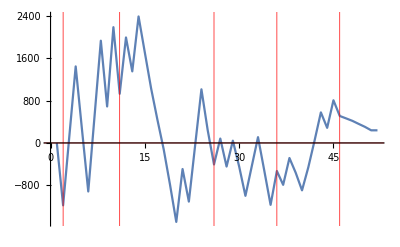

```mathematica
ListPlot[((Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify)//Coeff2Demo)//Accumulate,GridLines->{{2,11,26,36,46},{0}},GridLinesStyle->Red, Joined->True]
```

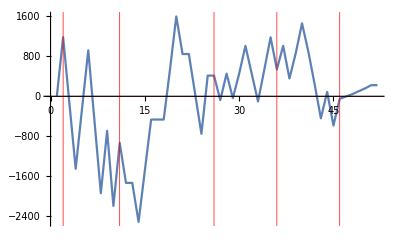

```mathematica
ListPlot[((Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify)//Coeff2Demo)//Accumulate,GridLines->{{2,11,26,36,46},{0}},GridLinesStyle->Red, Joined->True]
```

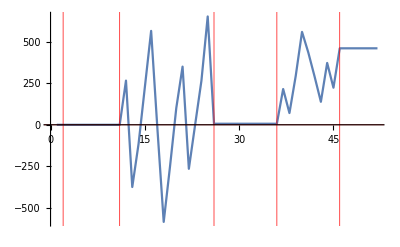

```mathematica
ListPlot[((Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify)//Coeff2Demo)//Accumulate,GridLines->{{2,11,26,36,46},{0}},GridLinesStyle->Red, Joined->True]
```

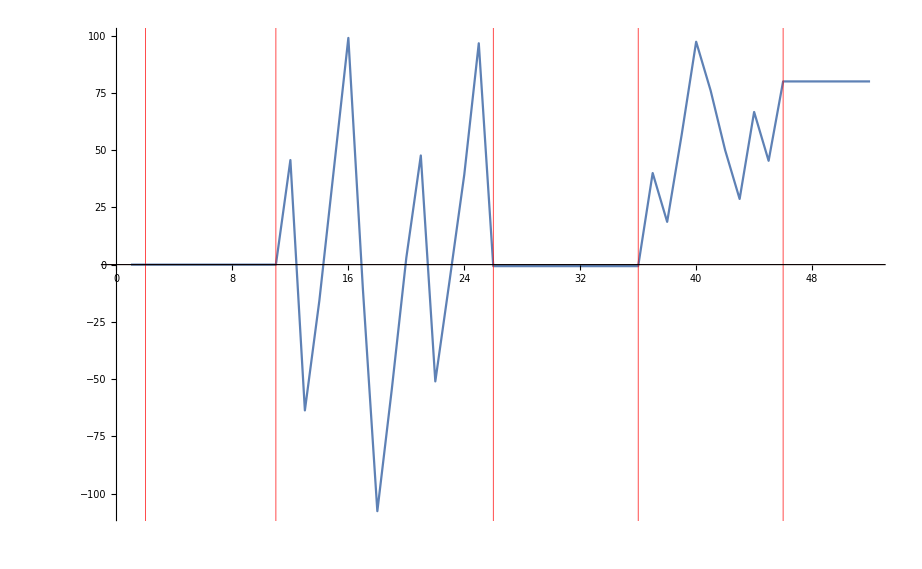

```mathematica
ListPlot[((Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify)//Coeff2Demo)//Accumulate,GridLines->{{2,11,26,36,46},{0}},GridLinesStyle->Red, Joined->True]
```

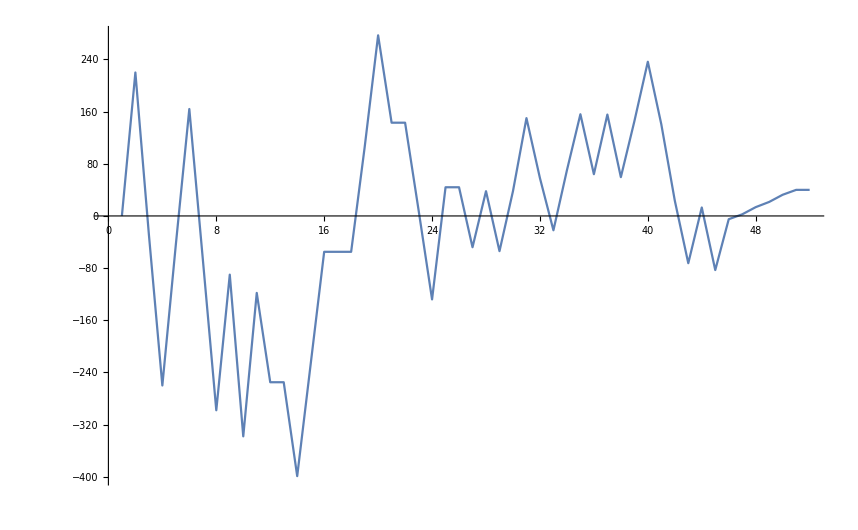

```mathematica
ListLinePlot[Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2Demo//Accumulate,GridLines->All]
```

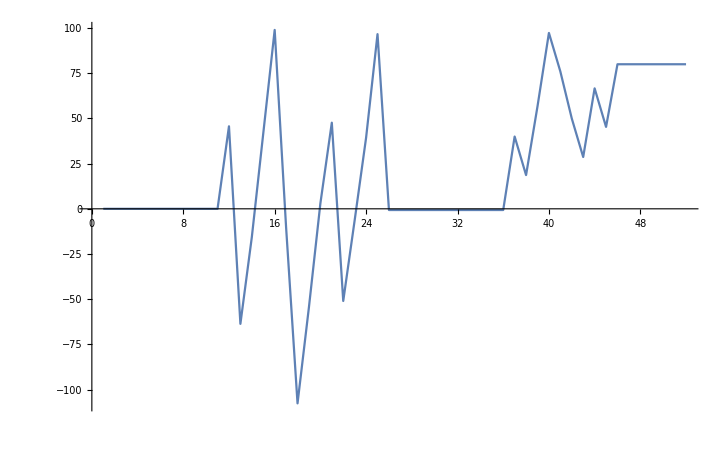

```mathematica
ListLinePlot[(Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify//Coeff2Demo//Accumulate)+(Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2Demo//Accumulate),GridLines->All]
```

```mathematica
Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2Demo
```

{0,220,-248,-232,216,208,-230,-232,208,-248,220,-137,0,-144,172,172,0,0,160,172,-134,0,-134,-137,172,0,-92,86,-92,92,112,-92,-80,92,86,-92,183/2,-96,171/2,183/2,-96,-117,-96,171/2,-96,78,15/2,11,8,11,15/2,0}

```mathematica
Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2//First
```

{-1/2,0,-1/2,1/2,1/2,0,0,1/2,1/2,-1/2,0,-1/2,-1/2,1/2,0}

```mathematica
Take[SortedNull,{1,1}]/.repcolofournullgraph2
```

{-Graphics-p1x2x3x4x50}

```mathematica
Take[SortedNull,{37,46}]/.repcolofournullgraph2
```

{-Graphics-p123x4526488,-Graphics-p124x3521954,-Graphics-p125x3420448,-Graphics-p12x34519696,-Graphics-p134x258784,-Graphics-p135x247374,-Graphics-p13x2456670,-Graphics-p145x233160,-Graphics-p14x2352460,-Graphics-p15x2341062}

```mathematica
Take[SortedNull,{27,36}]/.repcolofournullgraph2
```

{-Graphics-p123x4x526487,-Graphics-p124x3x521951,-Graphics-p125x3x420439,-Graphics-p134x2x58757,-Graphics-p135x2x47293,-Graphics-p145x2x32917,-Graphics-p1x234x5333,-Graphics-p1x235x4273,-Graphics-p1x245x3109,-Graphics-p1x2x34513}

```mathematica
Take[SortedNull,{12,26}]/.repcolofournullgraph2
```

{-Graphics-p12x34x519692,-Graphics-p12x35x419686,-Graphics-p12x3x4519684,-Graphics-p13x24x56642,-Graphics-p13x25x46588,-Graphics-p13x2x456562,-Graphics-p14x23x52430,-Graphics-p14x25x32214,-Graphics-p14x2x352190,-Graphics-p15x23x4972,-Graphics-p15x24x3810,-Graphics-p15x2x34738,-Graphics-p1x23x45244,-Graphics-p1x24x3584,-Graphics-p1x25x3436}

```mathematica
(Total[Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]//Simplify//Coeff2//First)+(Total[Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]]//Simplify//Coeff2//First)
```

```mathematica
{1/6,-1/3,1/6,1/6,1/6,-1/3,-1/3,1/6,1/6,1/6,-1/3,1/6,1/6,1/6,-1/3}
```

```mathematica
Take[SortedNull,{12,26}]
```

{p12x34x5,p12x35x4,p12x3x45,p13x24x5,p13x25x4,p13x2x45,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x23x45,p1x24x35,p1x25x34}

```mathematica
subset2=Select[AndToTable[ineqsnullSimpBis],SubsetQ[Take[SortedNull,{2,26}],ListofVars[#]]&]/.repcolofournullgraph2
```

{-Graphics-p12x3x4x519683>-Graphics-p12x34x519692,-Graphics-p12x3x4x519683>-Graphics-p12x35x419686,-Graphics-p12x3x4x519683>-Graphics-p12x3x4519684,-Graphics-p1x2x34x59>-Graphics-p12x34x519692,-Graphics-p1x2x35x43>-Graphics-p12x35x419686,-Graphics-p1x2x3x451>-Graphics-p12x3x4519684,-Graphics-p13x2x4x56561>-Graphics-p13x24x56642,-Graphics-p13x2x4x56561>-Graphics-p13x25x46588,-Graphics-p13x2x4x56561>-Graphics-p13x2x456562,-Graphics-p1x24x3x581>-Graphics-p13x24x56642,-Graphics-p1x25x3x427>-Graphics-p13x25x46588,-Graphics-p1x2x3x451>-Graphics-p13x2x456562,-Graphics-p14x2x3x52187>-Graphics-p14x23x52430,-Graphics-p14x2x3x52187>-Graphics-p14x25x32214,-Graphics-p14x2x3x52187>-Graphics-p14x2x352190,-Graphics-p1x23x4x5243>-Graphics-p14x23x52430,-Graphics-p1x25x3x427>-Graphics-p14x25x32214,-Graphics-p1x2x35x43>-Graphics-p14x2x352190,-Graphics-p15x2x3x4729>-Graphics-p15x23x4972,-Graphics-p15x2x3x4729>-Graphics-p15x24x3810,-Graphics-p15x2x3x4729>-Graphics-p15x2x34738,-Graphics-p1x23x4x5243>-Graphics-p15x23x4972,-Graphics-p1x24x3x581>-Graphics-p15x24x3810,-Graphics-p1x2x34x59>-Graphics-p15x2x34738,-Graphics-p1x23x4x5243>-Graphics-p1x23x45244,-Graphics-p1x2x3x451>-Graphics-p1x23x45244,-Graphics-p1x24x3x581>-Graphics-p1x24x3584,-Graphics-p1x2x35x43>-Graphics-p1x24x3584,-Graphics-p1x25x3x427>-Graphics-p1x25x3436,-Graphics-p1x2x34x59>-Graphics-p1x25x3436}